```mathematica
ClearAll["Global`*"]
```

```mathematica
rmax[v_,δ_,m_,omega_]=N[(√δ v^2)/(2 √(m^2-δ v^4)(omega-√(m^2-δ v^4)))];
ωmin[v_,δ_,m_]=N[√(m^2-δ v^4)];
```

```mathematica
Expand[(δ(z-v^2)^2+m^2-δ v^4)z]
```

```mathematica
ρ=12.01;
sol=ParametricNDSolve[{y''[r]+2/r y'[r]+ω^2 y[r]==(1-4 δ v^2 y[r]^2+3δ y[r]^4)y[r],y[10^-2]==y0-10^-4/6(ω^2 y0-(1-4 δ v^2 y0^2+3δ y0^4)y0),y'[ρ]==-(√(1-ω^2)+1/ρ)y[ρ]},y,{r,10^-2,ρ},{δ,v,ω,y0},WorkingPrecision->MachinePrecision(*,Method->"ImplicitRungeKutta"*)]
```

{y→ParametricFunction[<>]}

```mathematica
ListLinePlot[Table[{0.8+0.001i,Log[((y[0.6,1,0.93,0.8+0.001i][0.01+2 10^-2]-y[0.6,1,0.93,0.8+0.001i][0.01])/(2 10^-2))^2]/.sol},{i,0,100}]]
```

```mathematica
FindMinimum[Log[((y[0.6,1,ω,y0][0.01+2 10^-2]-y[0.6,1,ω,y0][0.01])/(2 10^-2))^2]/.ω->0.93/.sol,{y0,0.88}]
```

```mathematica
z[x_]:=y[0.6,1,0.93,0.8755167076959837][r]/.sol;
```

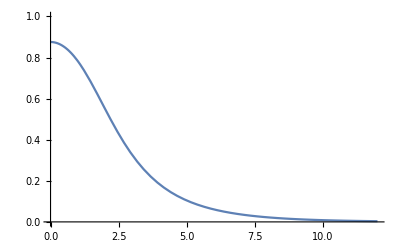

```mathematica
Plot[z[x],{r,0.01,12},PlotRange->{{0,12},{0,1}}]
```

```mathematica
f[r_]:=y[0.6,1,0.93,0.8755167076959837][r+0.01]/.sol;
```

```mathematica
QBfull[v_,δ_,omega_,dω_,L_,n_,Ωin_,Ωout_]:=(
R=L;
ω=omega;
h=R/n;
a=0;
a1[x_]:=1;
a2[x_]:=2/x;
a3[ω_]:=ω^2;
S[y_]:=(1-4 δ v^2 y^2+3δ y^4)y;
V[y_]:=y^2-2 δ v^2 y^4+δ y^6;
(*MAIN CYCLE*)
For[k=Ωin,k≤Ωout,k++,
eq[0]=(2/3 a3[0] h^2-6)c[0]+(6+(a3[0] h^2)/3) c[1]==h^2 S[2/3 c[0]+1/3 c[1]];
Table[p[i]=6 a1[a+i h]-3h a2[a+i h]+h^2 a3[ω],{i,1,n}];
Table[q[i]=-12 a1[a+i h]+4 h^2 a3[ω],{i,1,n}];
Table[r[i]=6 a1[a+i h]+3h a2[a+i h]+h^2 a3[ω],{i,1,n}];
Table[eq[i]=p[i]c[i-1]+q[i]c[i]+r[i]c[i+1]==6 h^2 S[1/6 c[i-1]+2/3 c[i]+1/6 c[i+1]],{i,1,n}];
eq[n+1]=(1/6(√(1-ω^2)+1/R)-1/(2h))c[n-1]+2/3(√(1-ω^2)+1/R)c[n]+(1/6(√(1-ω^2)+1/R)+1/(2 h))c[n+1]==0;
Table[iceq[i]=1/6 cc[i-1]+2/3 cc[i]+1/6 cc[i+1]==f[i h],{i,0,n}];
iceq[-1]=cc[-1]==cc[1]; iceq[n+1]=cc[n-1]==cc[n+1];
approx=Table[cc[j],{j,-1,n+1}]/.NSolve[Table[iceq[i],{i,-1,n+1}],Table[cc[j],{j,-1,n+1}]];
coef=Table[c[k],{k,0,n+1}]/.FindRoot[Table[eq[i],{i,0,n+1}],Table[{c[k],approx[[1,1+k]]},{k,0,n+1}](*,WorkingPrecision->100*)];
For[i=0,i≤n+1,i++,t[i]=coef[[i+1]]];
t[-1]=t[1];
ϕ=Table[{h i,1/6 t[i-1]+2/3 t[i]+1/6 t[i+1]},{i,0,n}];
(*profile[k]=Table[{h i,1/6 t[i-1]+2/3 t[i]+1/6 t[i+1]},{i,0,n}];*)
coefficients[k]=Table[{h i,t[i]},{i,-1,n+1}];
Q[k]=2 ω 4 π Sum[(h (i-1))^2 ϕ[[i,2]]^2,{i,1,n+1}];
H[k]=4 π Sum[(h (i-1))^2(((ϕ[[i+1,2]]-ϕ[[i-1,2]])/(2h))^2+ω^2 ϕ[[i,2]]^2+V[ϕ[[i,2]]]),{i,2,n}];
w[k]=ω;
dx[k]=h;
f[x_]:=Sum[t[i]BSplineBasis[{3,{a+(i-2)h,a+(i-1)h,a+i h,a+(i+1)h,a+(i+2)h}},0,x],{i,-1,n+1}];
(*Values for next iterration*)
ω=omega-dω (k-Ωin+1);
time=1;
While[ϕ[[time,2]]/ϕ[[1,2]]>10^-2,time++];
R=1.5(time-1)h;
box[k]=R;
h=R/n;
];
)
```

```mathematica
QBfull[1,0.6,0.92,0.002,12,400,0,120]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
{w[n],box[n]}/.n->120
```

{0.68,27.6173}

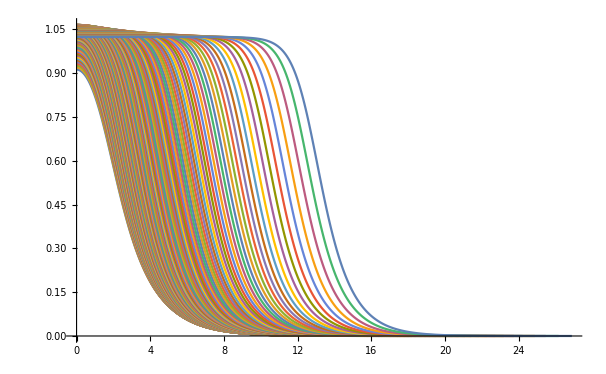

```mathematica
ListLinePlot[Table[Table[{coefficients[k][[i+1,1]],1/6(coefficients[k][[i,2]]+4coefficients[k][[i+1,2]]+coefficients[k][[i+2,2]])},{i,1,401}],{k,0,120}]]
```

```mathematica
f[x_]:=Sum[coefficients[30][[i+2,2]]BSplineBasis[{3,{a+(i-2)dx[10],a+(i-1)dx[10],a+i dx[10],a+(i+1)dx[10],a+(i+2)dx[10]}},0,x],{i,-1,400+1}];
```

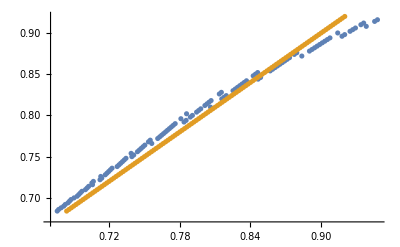

```mathematica
ListPlot[{Table[{(H[k+1]-H[k-1])/(Q[k+1]-Q[k-1]),w[k]},{k,2,118}],Table[{w[k],w[k]},{k,0,118}]},PlotRange->Full]
```

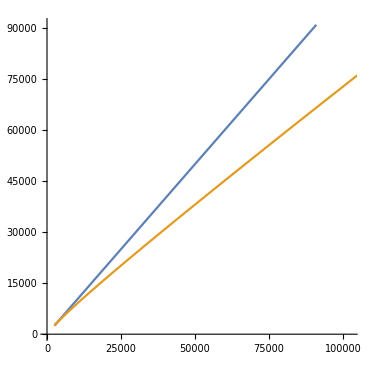

```mathematica
ListLinePlot[{Table[{Q[k],Q[k]},{k,0,120}],Table[{Q[k],H[k]},{k,0,120}]},AspectRatio->1]
```